```mathematica
∫_-1^2 (4-x^2)ⅆx
```

9

```mathematica
Integrate[4-x^2,{x,-1,2}]
```

9

```mathematica
a=-1;
b=2;
g=4-x^2;
∫_-1^2 gⅆx
```

9

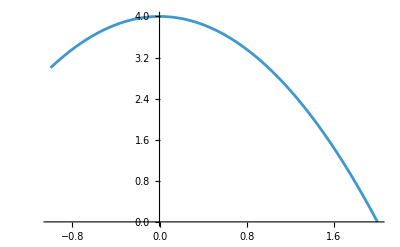

```mathematica
Plot[g, {x, a, b}]
```

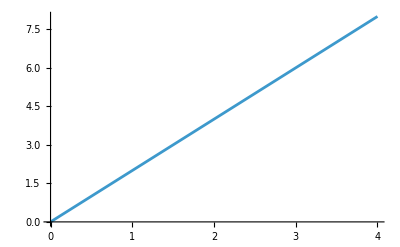

```mathematica
a=0;
b=4;
g=2x;
Plot[g, {x, a, b}]
```

```mathematica
∫_a^b gⅆx
```

16

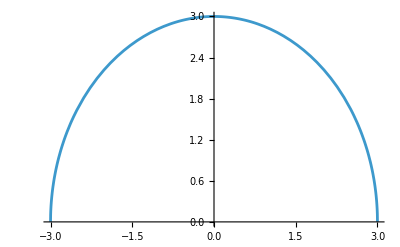

```mathematica
a=-3;
b=3;
g=Sqrt[9-x^2];
Plot[g, {x, a, b}]
```

```mathematica
∫_a^b gⅆx==Pi*3^2/2
∫_a^b gⅆx
```

True

(9 π)/2

```mathematica
(∫_a^b (x g)ⅆx)/∫_a^b gⅆx
```

0

```mathematica
Integrate[x g,{x,a,b}]/Integrate[g,{x,a,b}]
```

0

2/9

(2 x)/9

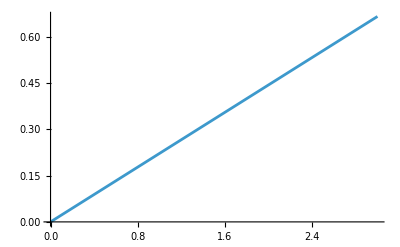

1

```mathematica
a=0;
b=3;
g=x;
Plot[g, {x, a, b}];
area=Integrate[g,{x,a,b}];
k=1/area
f=k*g
Plot[f, {x, a, b}]
area=Integrate[f,{x,a,b}]
```

1

1/4 (-2+x)

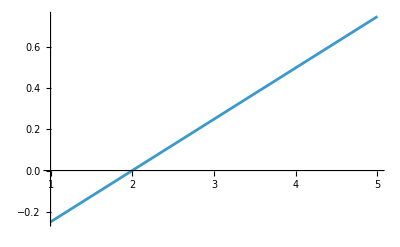

1

```mathematica
a=1;
b=5;
g=1/4*(x-2);
area=Integrate[g,{x,a,b}];
k=1/area
f=k*g
Plot[f, {x, a, b}]
area=Integrate[f,{x,a,b}]
```

1

(1+x)/8

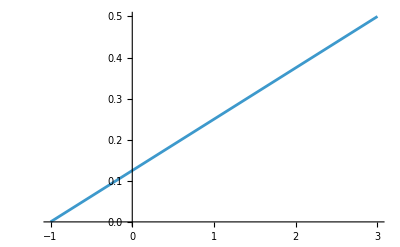

1

```mathematica
a=-1;
b=3;
g=1/8*(x+1);
area=Integrate[g,{x,a,b}];
k=1/area
f=k*g
Plot[f, {x, a, b}]
area=Integrate[f,{x,a,b}]
```